https://en.wikipedia.org/wiki/Fabry% E2 %80 %93 P % C3 % A9rot_interferometer
Finesse=Δλ/δλ where Δλ is the difference in wavelength between two peaks and δλ is the FWHM of the peaks

Finesse=π/(2 arcsin(1/(√CF))) where CF is the  coefficient of finesse.
CF=1/(Sin(π/(Finesse*2))^2)

Convert the measured finesse (from peak FWHM and the distance between peaks) to the coefficient of finesse

```mathematica
Finesse[CF_]:=π/(2 ArcSin[1/(√CF)])

CFinesse:=InverseFunction[Finesse] (*check that this is right using the inverse*)
N[CFinesse[200]]
CFinesse:=Function[fin,1/(Sin[π/(2 fin)])^2];
N[CFinesse[200]]
FPTrans=Function[{cfin,δ},1/(1+cfin* (Sin[δ/2])^2)];
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

16211.7

16211.7

normalize the transmission function so that the other peak is at x=1 and then plot

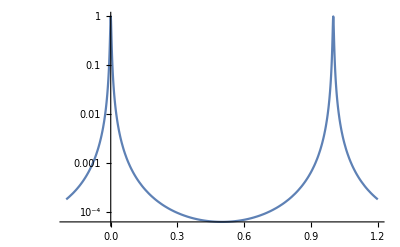

```mathematica
fineval=200;
LogPlot[FPTrans[CFinesse[fineval],x 2π],{x,-0.2,1.2},PlotRange->All]
```

Lets compute the integral about the middle of two peaks and compare it to the integral of the peak
The indefinite integral shows that there are some discontinuities in the antiderivative that we would be wise to sidestep

```mathematica
IndefMid=Integrate[FPTrans[CF,x π 2],x]
```

ArcTan[√(1+CF) Tan[π x]]/(√(1+CF) π)

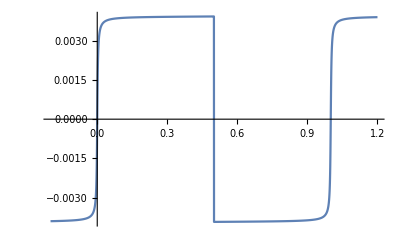

```mathematica
Plot[IndefMid/.{x->xv,CF->CFinesse[200]},{xv,-0.2,1.2},PlotRange->All]
```

Compute the definite integral for some width about the middle by taking only one side and using the symmetry of the function

```mathematica
IntMid=2*Integrate[FPTrans[CF,x 2 π],{x,1/2,1/2+wmid/2},Assumptions->{{CF,wmid}∈Reals && wmin>0 && wmin<1}]
```

ConditionalExpression[(π-2 ArcTan[√(1+CF) Cot[(π wmid)/2]])/(√(1+CF) π),C[1]∈ℤ&&C[2]∈ℤ&&wmid≥2 C[1]&&1+wmid≥2 C[2]&&C[1]≥0&&C[2]≥1]

```mathematica
IntMid=IntMid[[1]]
```

(π-2 ArcTan[√(1+CF) Cot[(π wmid)/2]])/(√(1+CF) π)

```mathematica
IntPeak=Integrate[FPTrans[CF,x 2 π],{x,-wpeak/2,+wpeak/2},Assumptions->{{CF,wmid}∈Reals && wpeak>0,wpeak<1}]
```

(2 ArcTan[√(1+CF) Tan[(π wpeak)/2]])/(√(1+CF) π)

```mathematica
fineval=200;
intδ=1/fineval;
N[IntPeak/.{CF->CFinesse[fineval],wpeak->intδ/200}]
N[IntMid/.{CF->CFinesse[fineval],wmid->intδ/200}]
NIntegrate[FPTrans[CFinesse[fineval],x 2π],{x,-intδ/2,intδ/2},WorkingPrecision->100]
NIntegrate[FPTrans[CFinesse[fineval],x  2π],{x,1/2-intδ/2,1/2+intδ/2}]
```

0.0000249998

1.542×10^-9

0.003926983538482524547992337284580827791287165274026658189240510148549662642850198723968682914366865842

3.08406×10^-7

```mathematica
PowerRatio=IntMid/IntPeak
```

(π-2 ArcTan[√(1+CF) Cot[(π wmid)/2]])/(2 ArcTan[√(1+CF) Tan[(π wpeak)/2]])

```mathematica
PowerRatio=(π-2 ArcTan[√(1+CF) Cot[(π wmid)/2]])/(2 ArcTan[√(1+CF) Tan[(π wpeak)/2]])
```

(π-2 ArcTan[√(1+CF) Cot[(π wmid)/2]])/(2 ArcTan[√(1+CF) Tan[(π wpeak)/2]])

In summary the ratio of the integrated power about the midpoint (of width wmid) to the power in the peak (of width wpeak) is
ConditionalExpression[-(π-2 ArcTan[√(1+CF) Cot[(π wmid)/2]])/(2 ArcTan[√(1+CF) Cot[(π wpeak)/2]]),You∉Fools]
The expression will not hold if you make wmid or wpeak too big, both wmid and wpeak are normalized such  that they are a fraction of the peak to peak width (which is unity)

```mathematica
ToExpression["\\text{ConditionalExpression}\\left[-\\frac{\\pi }{2 \\tan ^{-1}\\left(\\sqrt{\\text{CF}+1} \\cot \\left(\\frac{\\pi  \\text{wpeak}}{2}\\right)\\right)}",TeXForm,HoldForm]
```

ToExpression::esntx: Could not parse \text{ConditionalExpression}\left[-\frac{\pi }{2 \tan ^{-1}\left(\sqrt{\text{CF}+1} \cot \left(\frac{\pi  \text{wpeak}}{2}\right)\right)} as input.

$Failed

Compare num & analy integrations

```mathematica
fineval=200
PowerRatio/.{CF->CFinesse[fineval],wmid->0.1,wpeak->0.1}
```

200

0.00081768

Lets look at the behaviors normalizing the integration width to the FWHM of the peak

```mathematica
fineval=200
peakδ=10/fineval;
midδ=10/fineval;
Ppeak=NIntegrate[FPTrans[CFinesse[fineval],x 2π],{x,-peakδ/2,peakδ/2}]
Pmid=NIntegrate[FPTrans[CFinesse[fineval],x  2π],{x,1/2-midδ/2,1/2+midδ/2}]
Pmid/Ppeak
```

200

0.00735637

3.09035×10^-6

0.000420092

```mathematica
PRatioWidths:=Function[{fin,NormPeakδ,NormMidδ},Module[{peakδ,midδ},
peakδ=NormPeakδ/fin;
midδ=NormMidδ/fin;
Ppeak=NIntegrate[FPTrans[CFinesse[fin],x 2π],{x,-peakδ/2,peakδ/2}];
Pmid=NIntegrate[FPTrans[CFinesse[fin],x  2π],{x,1/2-midδ/2,1/2+midδ/2}];
Pmid/Ppeak]]
```

```mathematica
PRatioWidthsAnal:=Function[{fin,NormPeakδ,NormMidδ},Module[{peakδ,midδ},
peakδ=NormPeakδ/fin;
midδ=NormMidδ/fin;
PowerRatio/.{CF->CFinesse[fin],wpeak->peakδ,wmid->midδ}]]
```

```mathematica
fineval=200;
wtestpeak=10;
wtestmid=10;
PRatioWidths[fineval,wtestpeak,wtestmid]
N[PRatioWidthsAnal[fineval,wtestpeak,wtestmid]]
```

0.000420092

0.000420092

0.000420092

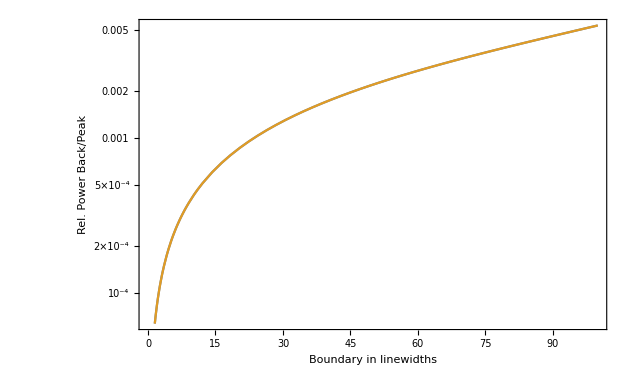

```mathematica
PRatioWidths[200,10,10]
LogPlot[{PRatioWidths[200,10,x],PRatioWidthsAnal[200,10,x]},{x,0,100},FrameLabel->{"Boundary in linewidths","Rel. Power Back/Peak"},Frame->True]
```